Tabla para que podamos comprobar si hay cambio de signo o no :

(1. | -1.
1.1 | -0.79
1.2 | -0.56
1.3 | -0.31
1.4 | -0.04
1.5 | 0.25
1.6 | 0.56
1.7 | 0.89
1.8 | 1.24
1.9 | 1.61
2. | 2.)

Iteración: 0  a= 1. b= 2. rn: 1.5 f[rn] = 0.25 Error: ∞[]

Iteración: 1  a= 1. b= 1.5 rn: 1.25 f[rn] = -0.4375 Error: 0.2

Iteración: 2  a= 1.25 b= 1.5 rn: 1.375 f[rn] = -0.109375 Error: 0.09090909091

Iteración: 3  a= 1.375 b= 1.5 rn: 1.4375 f[rn] = 0.0664063 Error: 0.04347826087

Iteración: 4  a= 1.375 b= 1.4375 rn: 1.40625 f[rn] = -0.0224609 Error: 0.02222222222

Iteración: 5  a= 1.40625 b= 1.4375 rn: 1.42188 f[rn] = 0.0217285 Error: 0.01098901099

Iteración: 6  a= 1.40625 b= 1.42188 rn: 1.41406 f[rn] = -0.000427246 Error: 0.005524861878

Iteración: 7  a= 1.41406 b= 1.42188 rn: 1.41797 f[rn] = 0.0106354 Error: 0.002754820937

Iteración: 8  a= 1.41406 b= 1.41797 rn: 1.41602 f[rn] = 0.00510025 Error: 0.001379310345

Iteración: 9  a= 1.41406 b= 1.41602 rn: 1.41504 f[rn] = 0.00233555 Error: 0.0006901311249

Iteración: 10  a= 1.41406 b= 1.41504 rn: 1.41455 f[rn] = 0.000953913 Error: 0.0003451846738

Iteración: 11  a= 1.41406 b= 1.41455 rn: 1.41431 f[rn] = 0.000263274 Error: 0.0001726221302

Iteración: 12  a= 1.41406 b= 1.41431 rn: 1.41418 f[rn] = -0.0000820011 Error: 0.00008631851532

Lo logré en la iteración : 12 con los datos:   a= 1.41418 b= 1.41431 Error: 0.00008631851532

La grafica de puntos es:

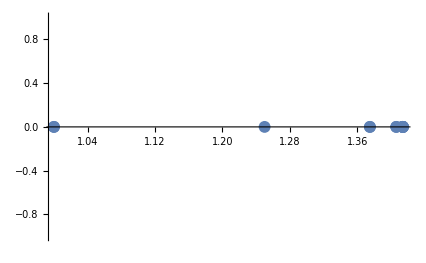

La grafica de la funcion es:

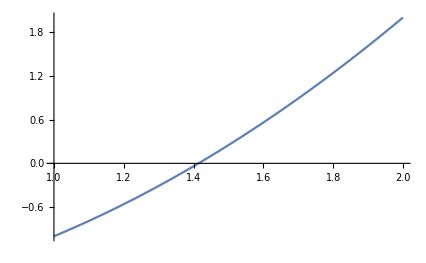

La union de ambas graficas:

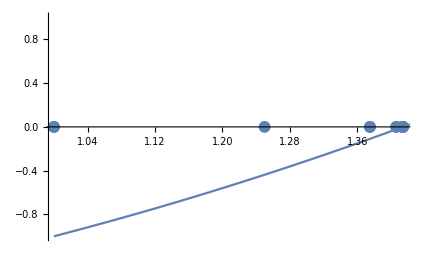

```mathematica
f[x_] =  (*x^3 + 4 * x^2 - 10 *)   Input["Digite la funcion"] ;

a =  Input["digite el invervalo inicial"];   (*Estos valores hay que darlos en double para que los resultados no dén en fraccionario *)
b = Input["digite el invervalo final"];
precision =  Input["digite la precision deseada"];(* 0.0001 *);
g2 = Plot[f[x], {x,a, b}];
coordenada = {};

(* Hallamos el valor aproximado del numero de iteraciones (Usando la formula vista en clase) *)
n = N[(Log[b - a] - Log[precision])/Log[2]];
Print["Tabla para que podamos comprobar si hay cambio de signo o no :"];
(* Hacemos la tabla con los valores a graficar de la funcion, para comprobar el cambio de signo *)
 Table[{x,f[x]},{x,a,b,0.1}]//MatrixForm
(* Inicializamos la variable rAnterior en 0, ya que inicialmente no disponemos de un rAnterior *)
rAnterior = 0;

(* El programa solo se ejecutará si cumple con las condiciones del TVI *)
If[f[a] * f[b] < 0 && Limit[f[x], x-> a] == f[a] && Limit[f[x], x -> b] == f[b],
For[i = 0, i ≤ n , i++,
(* Agregamos el valor de la coordenada actual en la variable coordenada, para poder graficar al final la lista de puntos hallados, hasta llegar al que acepte la tolerancia o de la raiz exacta *)
coordenada = Append[coordenada,{N[a], 0}];

(* Condicion normal, para cuando i > 0 (osea que tiene un dato anterior *)
If[i>0,
rAnterior = rActual;
rActual = (a + b)/2;

error = Abs[(rActual - rAnterior)/rActual];
Print["Iteración: ", i, "  a= ", N[a], " b= ",N[b] ," rn: ", N[rActual],  " f[rn] = ", N[f[rActual]], " Error: ", N[error, 10]];
];

(* Condicion para cuando i = 0, como no disponemos de un valor anterior, le damos al valor de error un valor de infinito y imprimimos los datos *)
If[i==0, 
error = Infinity[]; 
rActual = (a + b)/2;
Print["Iteración: ", i, "  a= ", N[a], " b= ",N[b] ," rn: ", N[rActual],  " f[rn] = ", N[f[rActual]], " Error: ", error];
];

(* Condiciones al evaluar el f[rActual] *)
If[f[rActual] > 0,
b = rActual ;, (* caso verdadero *)

a = rActual ; (*Caso falso *)
];

(* Cuando encontró un punto el cual cumple con la precision dada *)
If[error < precision  && i > 0,
Print["Lo logré en la iteración : ", i, " con los datos: ", "  a= ", N[a], " b= ",N[b] , " Error: ", N[error, 10]];
coordenada = Append[coordenada,{N[a], 0}];
Break[];
];  

(* Cuando encontró un punto que cumple con la precision dada según el usuario *)
If[f[rActual] == 0, 
Print["Encontré la raiz exacta: "]; 
coordenada = Append[coordenada,{N[a], 0}];
Print["Iteración: ", i, "  a= ", N[a], " b= ",N[b] ," rn: ", N[rActual],  " f[rn] = ", N[f[rActual]], " Error: ", N[error, 10]];
 Break[];
];
];,
Print["La funcion ingresada en 'a' y 'b' no satisface las condiciones del TVI"];
];
Print["La grafica de puntos es: "];
g1 = ListPlot[coordenada, PlotStyle->PointSize[0.02]];
g1
Print["La grafica de la funcion es: "];
g2

Print["La union de ambas graficas: "];
Show[g1,g2]
```